# Gravitational Waves

## Section 4.1 Generic Waveform

Power::infy: 碰到无穷表达式 1/0..

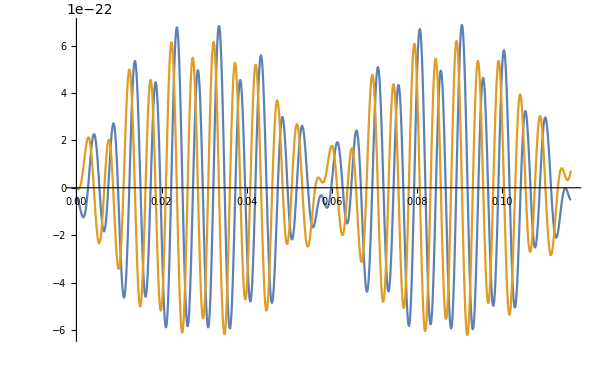

```mathematica
G=6.67*10^-8;
c=3*10^10;
r=3.0857*10^22;
i=π/6;(*inclination angle*)
n=1;(*number of free precession period *)
I0=10^45;(*moment of inertia*)
σ=π/4;(*initial wobble angle*)
ω0=100*2*π;(*initial angular velocity in body frame*)
I1=(1-0.18)*I0;
I2=I0*0.9;
I3=I0;
Δ1=I2-I3;
Δ2=I3-I1;
Δ3=I1-I2;
a=ω0*Sin[σ];
w20=0;
b=ω0*Cos[σ];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
dt=0.0001;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1+2*I*π/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
w1=Table[a*JacobiCN[t*taut,k2],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
time=Table[t,{t,0,n*T,dt}];
A11=2*(Δ2*w2^2-Δ3*w3^2);
A22=2*(Δ3*w3^2-Δ1*w1^2);
A33=2*(Δ1*w1^2-Δ2*w2^2);
A12=(Δ1-Δ2+Δ3^2/I3)w1*w2;
A21=A12;
A13=(Δ3-Δ1+Δ2^2/I2)w1*w3;
A31=A13;
A23=(Δ2-Δ3+Δ1^2/I1)w2*w3;
A32=A23;
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
cosϕ1=Cos[ArcCos[Table[Re[EllipticTheta[4,2*π/T*t+π*α*I,q]/EllipticTheta[4,2*π/T*t-π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ1=Sin[ArcSin[Table[Im[EllipticTheta[4,2*π/T*t+π*α*I,q]/EllipticTheta[4,2*π/T*t-π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ2=Table[Sin[(2π)/T1*t],{t,0,n*T,dt}];
cosϕ2=Table[Cos[(2π)/T1*t],{t,0,n*T,dt}];
cosϕ=cosϕ1*cosϕ2-sinϕ1*sinϕ2;
sinϕ=sinϕ1*cosϕ2+cosϕ1*sinϕ2;
R11=cosψ*cosϕ-cosθ*sinψ*sinϕ;
R12=-sinψ*cosϕ-cosθ*cosψ*sinϕ;
R13=sinθ*sinϕ;
R21=cosψ*sinϕ+cosθ*sinψ*cosϕ;
R22=-sinψ*sinϕ+cosθ*cosψ*cosϕ;
R23=-sinθ*cosϕ;
R31=sinθ*sinψ;
R32=sinθ*cosψ;
R33=cosθ;
plus11=((Cos[i]R21+Sin[i]R31)*(Cos[i]R21+Sin[i]R31)-R11*R11)*A11;
plus12=((Cos[i]R21+Sin[i]R31)*(Cos[i]R22+Sin[i]R32)-R11*R12)*A12;
plus13=((Cos[i]R21-Sin[i]R31)*(Cos[i]R23-Sin[i]R33)-R11*R13)*A13;
plus21=((Cos[i]R22+Sin[i]R32)*(Cos[i]R21+Sin[i]R31)-R12*R11)*A21;
plus22=((Cos[i]R22+Sin[i]R32)*(Cos[i]R22+Sin[i]R32)-R12*R12)*A22;
plus23=((Cos[i]R22-Sin[i]R32)*(Cos[i]R23-Sin[i]R33)-R12*R13)*A23;
plus31=((Cos[i]R23+Sin[i]R33)*(Cos[i]R21+Sin[i]R31)-R13*R11)*A31;
plus32=((Cos[i]R23+Sin[i]R33)*(Cos[i]R22+Sin[i]R32)-R13*R12)*A32;
plus33=((Cos[i]R23+Sin[i]R33)*(Cos[i]R23+Sin[i]R33)-R13*R13)*A33;
hplus=-G/(c^4 r)(plus11+plus12+plus13+plus21+plus22+plus23+plus31+plus32+plus33);
cross11=(Cos[i]R21+Sin[i]R31)*R11 *A11;
cross12=(Cos[i]R21+Sin[i]R31)*R12 *A12;
cross13=(Cos[i]R21+Sin[i]R31)*R13 *A13;
cross21=(Cos[i]R22+Sin[i]R32)*R11 *A21;
cross22=(Cos[i]R22+Sin[i]R32)*R12 *A22;
cross23=(Cos[i]R22+Sin[i]R32)*R13 *A23;
cross31=(Cos[i]R23+Sin[i]R33)*R11 *A31;
cross32=(Cos[i]R23+Sin[i]R33)*R12 *A32;
cross33=(Cos[i]R23+Sin[i]R33)*R13 *A33;
hcross=-(2G)/(c^4 r)(cross11+cross12+cross13+cross21+cross22+cross23+cross31+cross32+cross33);
first=Transpose@{time,hplus};
second=Transpose@{time,hcross};
large90=Transpose@{time,hplus,hcross};
ListPlot[{first,second},Joined->True]
```

```mathematica
T
```

0.116171

```mathematica
T1
```

0.00951364

## Section 4.2 Waveform for small oblatenesses, small wobble angles and small nonaxisymmetries

```mathematica
Clear["Global`*"]  (*Clear all variables*)
```

The expansion of Euler angles

```mathematica
cosϕ=Cos[t Subscript[Ω, 1]]
sinϕ=Sin[t Subscript[Ω, 1]]
cosθ=1-γ^2/2
sinθ=γ (1+8 κ Sin[t Subscript[Ω, 2]]^2)
cosψ=Sin[t Subscript[Ω, 2]]+(8 κ+32 κ^2) Cos[t Subscript[Ω, 2]]^2 Sin[t Subscript[Ω, 2]]+16 κ^2 Cos[t Subscript[Ω, 2]]^2 (1+3 Cos[2 t Subscript[Ω, 2]]) Sin[t Subscript[Ω, 2]]
sinψ=Cos[t Subscript[Ω, 2]]-(8 κ+32 κ^2) Cos[t Subscript[Ω, 2]] Sin[t Subscript[Ω, 2]]^2-96 κ^2 Cos[t Subscript[Ω, 2]]^3 Sin[t Subscript[Ω, 2]]^2
```

Cos[t Ω_1]

Sin[t Ω_1]

1-γ^2/2

γ (1+8 κ Sin[t Ω_2]^2)

Sin[t Ω_2]+(8 κ+32 κ^2) Cos[t Ω_2]^2 Sin[t Ω_2]+16 κ^2 Cos[t Ω_2]^2 (1+3 Cos[2 t Ω_2]) Sin[t Ω_2]

Cos[t Ω_2]-(8 κ+32 κ^2) Cos[t Ω_2] Sin[t Ω_2]^2-96 κ^2 Cos[t Ω_2]^3 Sin[t Ω_2]^2

```mathematica
R11=Expand[cosψ*cosϕ-cosθ*sinψ*sinϕ];
R12=Expand[-sinψ*cosϕ-cosθ*cosψ*sinϕ];

R13=Expand[sinθ*sinϕ];
R21=Expand[cosψ*sinϕ+cosθ*sinψ*cosϕ];
R22=Expand[-sinψ*sinϕ+cosθ*cosψ*cosϕ];
R23=Expand[-sinθ*cosϕ];
R31=Expand[sinθ*sinψ];
R32=Expand[sinθ*cosψ];
R33=Expand[cosθ];
w1=γ*b*Cos[Subscript[Ω, 2]*t];
w2=γ*b*Sin[Subscript[Ω, 2]*t]-γ*8*κ*b*Sin[Subscript[Ω, 2]*t];
w3=b;
Δ1=I2-I3;
Δ2=I3-I1;
Δ3=I1-I2;
A11=2*(Δ2*w2^2-Δ3*w3^2);
A22=2*(Δ3*w3^2-Δ1*w1^2);
A33=2*(Δ1*w1^2-Δ2*w2^2);
A12=(Δ1-Δ2)w1*w2;
A21=A12;
A13=(Δ3-Δ1)w1*w3;
A31=A13;
A23=(Δ2-Δ3)w2*w3;
A32=A23;
plus11=((Cos[i]R21+Sin[i]R31)*(Cos[i]R21+Sin[i]R31)-R11*R11)*A11;
plus12=((Cos[i]R21+Sin[i]R31)*(Cos[i]R22+Sin[i]R32)-R11*R12)*A12;
plus13=((Cos[i]R21+Sin[i]R31)*(Cos[i]R23+Sin[i]R33)-R11*R13)*A13;
plus21=((Cos[i]R22+Sin[i]R32)*(Cos[i]R21+Sin[i]R31)-R12*R11)*A21;
plus22=((Cos[i]R22+Sin[i]R32)*(Cos[i]R22+Sin[i]R32)-R12*R12)*A22;
plus23=((Cos[i]R22+Sin[i]R32)*(Cos[i]R23+Sin[i]R33)-R12*R13)*A23;
plus31=((Cos[i]R23+Sin[i]R33)*(Cos[i]R21+Sin[i]R31)-R13*R11)*A31;
plus32=((Cos[i]R23+Sin[i]R33)*(Cos[i]R22+Sin[i]R32)-R13*R12)*A32;
plus33=((Cos[i]R23+Sin[i]R33)*(Cos[i]R23+Sin[i]R33)-R13*R13)*A33;
hplus=-1/r(plus11+plus12+plus13+plus21+plus22+plus23+plus31+plus32+plus33);
```

### Plus polarization

the order of γ

```mathematica
p1=Simplify[Simplify[Coefficient[Expand[hplus],γ]/.κ->0]*γ]
```

(b^2 γ ((I1+I2-2 I3) Cos[t Ω_1]+(I1-I2) Cos[t (Ω_1-2 Ω_2)]) Sin[2 i])/(2 r)

the order of κ

```mathematica
Simplify[Simplify[Coefficient[Expand[hplus],κ]/.γ->0]*κ]
```

(8 b^2 (I1-I2) κ (3+Cos[2 i]) Sin[2 t (Ω_1-Ω_2)] Sin[2 t Ω_2])/r

```mathematica
TrigReduce[Sin[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])] Sin[2 t Subscript[Ω, 2]]]
```

1/2 (Cos[2 t (Ω_1-Ω_2)-2 t Ω_2]-Cos[2 t (Ω_1-Ω_2)+2 t Ω_2])

```mathematica
p2=(8 b^2 (I1-I2) κ (3+Cos[2 i]))/r*1/2 (Cos[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])-2 t Subscript[Ω, 2]]-Cos[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])+2 t Subscript[Ω, 2]])
```

(4 b^2 (I1-I2) κ (3+Cos[2 i]) (Cos[2 t (Ω_1-Ω_2)-2 t Ω_2]-Cos[2 t (Ω_1-Ω_2)+2 t Ω_2]))/r

The order of κ^2

```mathematica
Simplify[Simplify[Coefficient[Expand[hplus]/.γ-> 0,κ^2]]]*κ^2
```

(32 b^2 (I1-I2) κ^2 (3+Cos[2 i]) (Sin[2 t (Ω_1-2 Ω_2)]+2 Sin[2 t (Ω_1-Ω_2)]) Sin[2 t Ω_2])/r

Note that (I_1-I_2) already in the order of κ, this term is in the order of κ^3. We can drop it.

The order of γκ

```mathematica
Simplify[Simplify[Coefficient[Expand[hplus],γ*κ]]]*γ*κ
```

1/r 2 b^2 γ κ Sin[2 i] Sin[t Ω_2] ((I1-I2) Sin[t (Ω_1-3 Ω_2)]+6 (3 I1-2 I2-I3) Sin[t (Ω_1-Ω_2)]+(I1+I2-2 I3) Sin[t (Ω_1+Ω_2)])

```mathematica
1/r 2 b^2 γ κ Sin[2 i] Sin[t Subscript[Ω, 2]] (6 ( I1-I3) Sin[t (Subscript[Ω, 1]-Subscript[Ω, 2])]+(I1+I2-2 I3) Sin[t (Subscript[Ω, 1]+Subscript[Ω, 2])])
```

(2 b^2 γ κ Sin[2 i] Sin[t Ω_2] (6 (I1-I3) Sin[t (Ω_1-Ω_2)]+(I1+I2-2 I3) Sin[t (Ω_1+Ω_2)]))/r

```mathematica
(2 b^2 γ κ Sin[2 i] Sin[t Subscript[Ω, 2]] (6 (I1-I3) Sin[t (Subscript[Ω, 1]-Subscript[Ω, 2])]))/r
```

(12 b^2 (I1-I3) γ κ Sin[2 i] Sin[t (Ω_1-Ω_2)] Sin[t Ω_2])/r

```mathematica
TrigReduce[Sin[t (Subscript[Ω, 1]-Subscript[Ω, 2])] Sin[t Subscript[Ω, 2]]]
```

1/2 (Cos[t (Ω_1-Ω_2)-t Ω_2]-Cos[t (Ω_1-Ω_2)+t Ω_2])

```mathematica
p3=(12 b^2 (I1-I3) γ κ Sin[2 i])/r 1/2 (Cos[t (Subscript[Ω, 1]-Subscript[Ω, 2])-t Subscript[Ω, 2]])
```

(6 b^2 (I1-I3) γ κ Cos[t (Ω_1-Ω_2)-t Ω_2] Sin[2 i])/r

```mathematica
(2 b^2 γ κ Sin[2 i] Sin[t Subscript[Ω, 2]] ((I1+I2-2 I3) Sin[t (Subscript[Ω, 1]+Subscript[Ω, 2])]))/r
```

(2 b^2 (I1+I2-2 I3) γ κ Sin[2 i] Sin[t Ω_2] Sin[t (Ω_1+Ω_2)])/r

```mathematica
TrigReduce[Sin[t Subscript[Ω, 2]] Sin[t (Subscript[Ω, 1]+Subscript[Ω, 2])]]
```

1/2 (Cos[t Ω_2-t (Ω_1+Ω_2)]-Cos[t Ω_2+t (Ω_1+Ω_2)])

```mathematica
p4=(2 b^2 (I1+I2-2 I3) γ κ Sin[2 i])/r 1/2 (-Cos[t Subscript[Ω, 2]+t (Subscript[Ω, 1]+Subscript[Ω, 2])])
```

-(b^2 (I1+I2-2 I3) γ κ Cos[t Ω_2+t (Ω_1+Ω_2)] Sin[2 i])/r

The order of γ^2

```mathematica
Simplify[Simplify[Coefficient[Expand[hplus],γ^2]/.κ->0]*γ^2]
```

-(b^2 γ^2 (3+Cos[2 i]) ((I1+I2-2 I3) Cos[2 t Ω_1]+(-I1+I2) Cos[2 t (Ω_1-Ω_2)]))/(2 r)

```mathematica
p5=-(b^2 γ^2 (3+Cos[2 i]) ((I1+I2-2 I3) Cos[2 t Subscript[Ω, 1]]))/(2 r)
```

-(b^2 (I1+I2-2 I3) γ^2 (3+Cos[2 i]) Cos[2 t Ω_1])/(2 r)

```mathematica
p6=Simplify[Expand[hplus]/.{κ->0, γ-> 0}]
```

(b^2 (I1-I2) (3+Cos[2 i]) Cos[2 t (Ω_1-Ω_2)])/r

```mathematica
p1
p2
p3
p4
p5
p6
```

(b^2 γ ((I1+I2-2 I3) Cos[t Ω_1]+(I1-I2) Cos[t (Ω_1-2 Ω_2)]) Sin[2 i])/(2 r)

(4 b^2 (I1-I2) κ (3+Cos[2 i]) (Cos[2 t (Ω_1-Ω_2)-2 t Ω_2]-Cos[2 t (Ω_1-Ω_2)+2 t Ω_2]))/r

(6 b^2 (I1-I3) γ κ Cos[t (Ω_1-Ω_2)-t Ω_2] Sin[2 i])/r

-(b^2 (I1+I2-2 I3) γ κ Cos[t Ω_2+t (Ω_1+Ω_2)] Sin[2 i])/r

-(b^2 (I1+I2-2 I3) γ^2 (3+Cos[2 i]) Cos[2 t Ω_1])/(2 r)

(b^2 (I1-I2) (3+Cos[2 i]) Cos[2 t (Ω_1-Ω_2)])/r

The emission at Ω_1

```mathematica
hp1=Simplify[(b^2 γ ((I1+I2-2 I3) Cos[t Subscript[Ω, 1]]) Sin[2 i])/(2 r)/.I1+I2-2 I3->-2I3*ϵ]
```

-(b^2 I3 γ ϵ Cos[t Ω_1] Sin[2 i])/r

The emission at 2Ω_1-2Ω_2

```mathematica
hp2=(b^2 (I1-I2) (3+Cos[2 i]) Cos[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])])/r/.{I1-I2-> -16κ*ϵ*I3,3+Cos[2 i]-> 2(1+Cos[i]^2) }
```

-(32 b^2 I3 ϵ κ (1+Cos[i]^2) Cos[2 t (Ω_1-Ω_2)])/r

The emission at 2Ω_1

```mathematica
hp31=(4 b^2 (I1-I2) κ (3+Cos[2 i]) (-Cos[2 t Subscript[Ω, 1]]))/r/.{I1-I2-> -16κ*ϵ*I3,3+Cos[2 i]-> 2(1+Cos[i]^2)}
```

(128 b^2 I3 ϵ κ^2 (1+Cos[i]^2) Cos[2 t Ω_1])/r

```mathematica
hp32=-(b^2 (I1+I2-2 I3) γ^2 (3+Cos[2 i]) Cos[2 t Subscript[Ω, 1]])/(2 r)/.{I1+I2-2 I3->-2I3*ϵ,3+Cos[2 i]-> 2(1+Cos[i]^2)}
```

(2 b^2 I3 γ^2 ϵ (1+Cos[i]^2) Cos[2 t Ω_1])/r

```mathematica
hp3=hp31+hp32
```

(2 b^2 I3 γ^2 ϵ (1+Cos[i]^2) Cos[2 t Ω_1])/r+(128 b^2 I3 ϵ κ^2 (1+Cos[i]^2) Cos[2 t Ω_1])/r

The emission at Ω_1-2Ω_2

```mathematica
hp4=
((b^2 γ ((I1-I2) Cos[t (Subscript[Ω, 1]-2 Subscript[Ω, 2])]) Sin[2 i])/(2 r)+(6 b^2 (I1-I3) γ κ Cos[t (Subscript[Ω, 1]-2 Subscript[Ω, 2])] Sin[2 i])/r)/.{I1-I2-> -16κ*ϵ*I3,I1-I3-> -ϵ*I3}
```

-(14 b^2 I3 γ ϵ κ Cos[t (Ω_1-2 Ω_2)] Sin[2 i])/r

The emission at Ω_1+2Ω_2

```mathematica
hp5=-(b^2 (I1+I2-2 I3) γ κ Cos[t Subscript[Ω, 2]+t (Subscript[Ω, 1]+Subscript[Ω, 2])] Sin[2 i])/r/.{I1+I2-2 I3->-2I3*ϵ}
```

(2 b^2 I3 γ ϵ κ Cos[t Ω_2+t (Ω_1+Ω_2)] Sin[2 i])/r

The emission at 2 Ω_1-4Ω_2

```mathematica
hp6=(4 b^2 (I1-I2) κ (3+Cos[2 i]) (Cos[2 t (Subscript[Ω, 1]-2 Subscript[Ω, 2])]))/r/.{I1-I2-> -16κ*ϵ*I3,3+Cos[2 i]-> 2(1+Cos[i]^2)}
```

-(128 b^2 I3 ϵ κ^2 (1+Cos[i]^2) Cos[2 t (Ω_1-2 Ω_2)])/r

## The waveform for plus-polarized GWs

```mathematica
hp1
hp2
hp3
hp4
hp5
hp6
```

-(b^2 I3 γ ϵ Cos[t Ω_1] Sin[2 i])/r

-(32 b^2 I3 ϵ κ (1+Cos[i]^2) Cos[2 t (Ω_1-Ω_2)])/r

(2 b^2 I3 γ^2 ϵ (1+Cos[i]^2) Cos[2 t Ω_1])/r+(128 b^2 I3 ϵ κ^2 (1+Cos[i]^2) Cos[2 t Ω_1])/r

-(14 b^2 I3 γ ϵ κ Cos[t (Ω_1-2 Ω_2)] Sin[2 i])/r

(2 b^2 I3 γ ϵ κ Cos[t Ω_2+t (Ω_1+Ω_2)] Sin[2 i])/r

-(128 b^2 I3 ϵ κ^2 (1+Cos[i]^2) Cos[2 t (Ω_1-2 Ω_2)])/r

### Cross polarization

```mathematica
cross11=(Cos[i]R21+Sin[i]R31)*R11 *A11;
cross12=(Cos[i]R21+Sin[i]R31)*R12 *A12;
cross13=(Cos[i]R21+Sin[i]R31)*R13 *A13;
cross21=(Cos[i]R22+Sin[i]R32)*R11 *A21;
cross22=(Cos[i]R22+Sin[i]R32)*R12 *A22;
cross23=(Cos[i]R22+Sin[i]R32)*R13 *A23;
cross31=(Cos[i]R23+Sin[i]R33)*R11 *A31;
cross32=(Cos[i]R23+Sin[i]R33)*R12 *A32;
cross33=(Cos[i]R23+Sin[i]R33)*R13 *A33;
hcross=-2/r(cross11+cross12+cross13+cross21+cross22+cross23+cross31+cross32+cross33);
```

The order of γ

```mathematica
c1=Simplify[Simplify[Coefficient[Expand[hcross],γ]/.κ->0]*γ]
```

-(b^2 γ Sin[i] ((I1+I2-2 I3) Sin[t Ω_1]+(I1-I2) Sin[t (Ω_1-2 Ω_2)]))/r

The order of κ

```mathematica
Simplify[Simplify[Coefficient[Expand[hcross],κ]/.γ->0]*κ]
```

(32 b^2 (I1-I2) κ Cos[i] Cos[2 t (Ω_1-Ω_2)] Sin[2 t Ω_2])/r

```mathematica
TrigReduce[Cos[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])] Sin[2 t Subscript[Ω, 2]]]
```

1/2 (-Sin[2 t (Ω_1-Ω_2)-2 t Ω_2]+Sin[2 t (Ω_1-Ω_2)+2 t Ω_2])

```mathematica
c2=(32 b^2 (I1-I2) κ Cos[i])/r*1/2 (-Sin[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])-2 t Subscript[Ω, 2]]+Sin[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])+2 t Subscript[Ω, 2]])
```

(16 b^2 (I1-I2) κ Cos[i] (-Sin[2 t (Ω_1-Ω_2)-2 t Ω_2]+Sin[2 t (Ω_1-Ω_2)+2 t Ω_2]))/r

The order of κγ

```mathematica
Simplify[Simplify[Coefficient[Expand[hcross],γ*κ]]]*γ*κ
```

1/r 4 b^2 γ κ ((I1-I2) Cos[t (Ω_1-3 Ω_2)]+6 (3 I1-2 I2-I3) Cos[t (Ω_1-Ω_2)]+(I1+I2-2 I3) Cos[t (Ω_1+Ω_2)]) Sin[i] Sin[t Ω_2]

```mathematica
1/r 4 b^2 γ κ (6 (I1-I3) Cos[t (Subscript[Ω, 1]-Subscript[Ω, 2])]+(I1+I2-2 I3) Cos[t (Subscript[Ω, 1]+Subscript[Ω, 2])]) Sin[i] Sin[t Subscript[Ω, 2]]
```

(4 b^2 γ κ (6 (I1-I3) Cos[t (Ω_1-Ω_2)]+(I1+I2-2 I3) Cos[t (Ω_1+Ω_2)]) Sin[i] Sin[t Ω_2])/r

```mathematica
(4 b^2 γ κ (6 (I1-I3) Cos[t (Subscript[Ω, 1]-Subscript[Ω, 2])]) Sin[i] Sin[t Subscript[Ω, 2]])/r
```

(24 b^2 (I1-I3) γ κ Cos[t (Ω_1-Ω_2)] Sin[i] Sin[t Ω_2])/r

```mathematica
TrigReduce[Cos[t (Subscript[Ω, 1]-Subscript[Ω, 2])]  Sin[t Subscript[Ω, 2]]]
```

1/2 (-Sin[t (Ω_1-Ω_2)-t Ω_2]+Sin[t (Ω_1-Ω_2)+t Ω_2])

```mathematica
c3=(24 b^2 (I1-I3) γ κ  Sin[i])/r 1/2 (-Sin[t (Subscript[Ω, 1]-Subscript[Ω, 2])-t Subscript[Ω, 2]])
```

-(12 b^2 (I1-I3) γ κ Sin[i] Sin[t (Ω_1-Ω_2)-t Ω_2])/r

```mathematica
(4 b^2 γ κ ((I1+I2-2 I3) Cos[t (Subscript[Ω, 1]+Subscript[Ω, 2])]) Sin[i] Sin[t Subscript[Ω, 2]])/r
```

(4 b^2 (I1+I2-2 I3) γ κ Cos[t (Ω_1+Ω_2)] Sin[i] Sin[t Ω_2])/r

```mathematica
TrigReduce[Cos[t (Subscript[Ω, 1]+Subscript[Ω, 2])]  Sin[t Subscript[Ω, 2]]]
```

1/2 (Sin[t Ω_2-t (Ω_1+Ω_2)]+Sin[t Ω_2+t (Ω_1+Ω_2)])

```mathematica
c4=(4 b^2 (I1+I2-2 I3) γ κ  Sin[i])/r 1/2 (Sin[t Subscript[Ω, 2]+t (Subscript[Ω, 1]+Subscript[Ω, 2])])
```

(2 b^2 (I1+I2-2 I3) γ κ Sin[i] Sin[t Ω_2+t (Ω_1+Ω_2)])/r

The order of γ^2

```mathematica
Simplify[Simplify[Coefficient[Expand[hcross],γ^2]/.κ->0]*γ^2]
```

(2 b^2 γ^2 Cos[i] ((I1+I2-2 I3) Sin[2 t Ω_1]+(-I1+I2) Sin[2 t (Ω_1-Ω_2)]))/r

```mathematica
c5=(2 b^2 γ^2 Cos[i] ((I1+I2-2 I3) Sin[2 t Subscript[Ω, 1]]))/r
```

(2 b^2 (I1+I2-2 I3) γ^2 Cos[i] Sin[2 t Ω_1])/r

```mathematica
c6=Simplify[Expand[hcross]/.{κ->0, γ-> 0}]
```

-(4 b^2 (I1-I2) Cos[i] Sin[2 t (Ω_1-Ω_2)])/r

```mathematica
c1
c2
c3
c4
c5
c6
```

-(b^2 γ Sin[i] ((I1+I2-2 I3) Sin[t Ω_1]+(I1-I2) Sin[t (Ω_1-2 Ω_2)]))/r

(16 b^2 (I1-I2) κ Cos[i] (-Sin[2 t (Ω_1-Ω_2)-2 t Ω_2]+Sin[2 t (Ω_1-Ω_2)+2 t Ω_2]))/r

-(12 b^2 (I1-I3) γ κ Sin[i] Sin[t (Ω_1-Ω_2)-t Ω_2])/r

(2 b^2 (I1+I2-2 I3) γ κ Sin[i] Sin[t Ω_2+t (Ω_1+Ω_2)])/r

(2 b^2 (I1+I2-2 I3) γ^2 Cos[i] Sin[2 t Ω_1])/r

-(4 b^2 (I1-I2) Cos[i] Sin[2 t (Ω_1-Ω_2)])/r

Emission at Ω_1

```mathematica
hc1=Simplify[-(b^2 γ Sin[i] ((I1+I2-2 I3) Sin[t Subscript[Ω, 1]]))/r/.I1+I2-2 I3->-2I3*ϵ]
```

(2 b^2 I3 γ ϵ Sin[i] Sin[t Ω_1])/r

The emission at 2Ω_1-2Ω_2

```mathematica
hc2=-(4 b^2 (I1-I2) Cos[i] Sin[2 t (Subscript[Ω, 1]-Subscript[Ω, 2])])/r/.{I1-I2-> -16κ*ϵ*I3 }
```

(64 b^2 I3 ϵ κ Cos[i] Sin[2 t (Ω_1-Ω_2)])/r

The emission at 2Ω_1

```mathematica
hc3=((2 b^2 (I1+I2-2 I3) γ^2 Cos[i] Sin[2 t Subscript[Ω, 1]])/r+(16 b^2 (I1-I2) κ Cos[i] (Sin[2 t Subscript[Ω, 1]]))/r)/.{I1+I2-2 I3->-2I3*ϵ, I1-I2-> -16κ*ϵ*I3}
```

-(4 b^2 I3 γ^2 ϵ Cos[i] Sin[2 t Ω_1])/r-(256 b^2 I3 ϵ κ^2 Cos[i] Sin[2 t Ω_1])/r

The emission at Ω_1-2Ω_2

```mathematica
hc4=(-(b^2 γ Sin[i] ((I1-I2) Sin[t (Subscript[Ω, 1]-2 Subscript[Ω, 2])]))/r-(12 b^2 (I1-I3) γ κ Sin[i] Sin[t (Subscript[Ω, 1]-2 Subscript[Ω, 2])])/r)/.{I1-I2-> -16κ*ϵ*I3, I1-I3-> -I3*ϵ}
```

(28 b^2 I3 γ ϵ κ Sin[i] Sin[t (Ω_1-2 Ω_2)])/r

The emission at Ω_1+2Ω_2

```mathematica
hc5=(2 b^2 (I1+I2-2 I3) γ κ Sin[i] Sin[t Subscript[Ω, 2]+t (Subscript[Ω, 1]+Subscript[Ω, 2])])/r/.I1+I2-2 I3->-2I3*ϵ
```

-(4 b^2 I3 γ ϵ κ Sin[i] Sin[t Ω_2+t (Ω_1+Ω_2)])/r

The emission 2Ω_1-4Ω_2

```mathematica
hc6=(16 b^2 (I1-I2) κ Cos[i] (-Sin[2 t (Subscript[Ω, 1]-2 Subscript[Ω, 2])]))/r/.I1-I2-> -16κ*ϵ*I3
```

(256 b^2 I3 ϵ κ^2 Cos[i] Sin[2 t (Ω_1-2 Ω_2)])/r

## The waveform for cross-polarized GWs

```mathematica
hc1
hc2
hc3
hc4
hc5
hc6
```

(2 b^2 I3 γ ϵ Sin[i] Sin[t Ω_1])/r

(64 b^2 I3 ϵ κ Cos[i] Sin[2 t (Ω_1-Ω_2)])/r

-(4 b^2 I3 γ^2 ϵ Cos[i] Sin[2 t Ω_1])/r-(256 b^2 I3 ϵ κ^2 Cos[i] Sin[2 t Ω_1])/r

(28 b^2 I3 γ ϵ κ Sin[i] Sin[t (Ω_1-2 Ω_2)])/r

-(4 b^2 I3 γ ϵ κ Sin[i] Sin[t Ω_2+t (Ω_1+Ω_2)])/r

(256 b^2 I3 ϵ κ^2 Cos[i] Sin[2 t (Ω_1-2 Ω_2)])/r

## Section 5 Discussion and the order of magnitudes analyse

```mathematica
ϵ=10^-7;
I3=10^45;
b=100.0*2*π;
G=6.67*10^-8;
c=3*10^10;
r=3.0857*10^22;
G/c^4*hc1
G/c^4*hc2
Simplify[G/c^4*hc3]
G/c^4*hc4
G/c^4*hc5
G/c^4*hc6
```

2.10706×10^-28 γ Sin[i] Sin[t Ω_1]

6.74259×10^-27 κ Cos[i] Sin[2 t (Ω_1-Ω_2)]

(-4.21412×10^-28 γ^2-2.69704×10^-26 κ^2) Cos[i] Sin[2 t Ω_1]

2.94988×10^-27 γ κ Sin[i] Sin[t (Ω_1-2 Ω_2)]

-4.21412×10^-28 γ κ Sin[i] Sin[t Ω_2+t (Ω_1+Ω_2)]

2.69704×10^-26 κ^2 Cos[i] Sin[2 t (Ω_1-2 Ω_2)]